P. Huft
My notebook for converting the H.-L. eqs. for an atom interacting with a propagating quantized electric field into the Linblad form with the density operator. See the paper by Scarani.

## definitions

```mathematica
(*the Schrodinger picture operators, or equivalently the Heisenberg ops at t=t0*)
σ0=PauliMatrix[0];
σx=PauliMatrix[1];
σy=PauliMatrix[2];
σz=PauliMatrix[3];
σp=1/2(σx+I σy);
σm=1/2(σx-I σy);
a=σm;
adag=σp;
dag[z_]=ConjugateTranspose[z];

(*operators in the atom-field space with the Fock state basis truncated at N=1*)
aa=KroneckerProduct[a,σ0];
sm=KroneckerProduct[σ0,σm];
sp=dag[sm];
sz=KroneckerProduct[σ0,σz];
II=KroneckerProduct[σ0,σ0];

BuildMasterEq[ρ0_,H_, Llist_,t0_:0]:=Module[{dim,rho,eqIdcs,comm,linblad,rhoPruned,eqsPruned,rhoICPruned, popIdxList, cohIdxList, i, j,m,L},
(*The code below builds the equations to be passed to NDSolve, removing the redundant equations (since Subscript[ρ, ij]=Subscript[ρ, ji]^*).

"Pruned" variables refer to the eqs which have had the redundant elements removed.

Args: 
 ρ0: the initial density matrix;
	H: the Hamiltonian;
	L: the jump operators. I assume that decay constants γ are accounted for in L, which is to say that the Linblad term looks like (L ρ L^†-1/2(ρ L^†L +L^†L ρ)) rather than γ(L ρ L^†-1/2(ρ L^†L +L^†L ρ));
	t0: the initial time, which is 0 if not specified.

Returns: eqsPruned, rhoICPruned (the pruned initial state), rhoPruned (the pruned set of variables, i.e. elements of ρ, to solve for), popIdxList (the indices of the population terms), cohIdxList (inds of the coherence terms)
*)
Clear[ρ,t];
dim = Length[H];
rho=Array[Subscript[ρ, #1,#2][t]&,{dim,dim}];
(*enforce conjugate relationship of ρ's off-diagonals *)
eqIdcs = {};
For[i=1,i<dim+1,i++,
For[j=dim,j>i,j--,
rho[[j,i]] = Conjugate[rho[[i,j]]];
AppendTo[eqIdcs,{i,j}]
]
];
(*generate non-redundant eqs and initial conditions*)
comm =  H.rho-rho.H  ;
linblad=Array[0&,{dim,dim}];
For[m=1,m<Length[Llist]+1,m++,
L=Llist[[m]];
linblad +=L.rho.dag[L]-1/2(dag[L].L.rho + rho.dag[L].L);
];
(*linblad =L.rho.dag[L]-1/2(dag[L].L.rho + rho.dag[L].L);*)
rhoPruned ={};
eqsPruned = {};
rhoICPruned = {};
For[i=1,i<dim+1,i++,
For[j=1,j<dim+1,j++,
If[i<=j,
AppendTo[eqsPruned,D[rho[[i,j]],t]==-I comm[[i,j]]+linblad[[i,j]]];
AppendTo[rhoICPruned,(rho/.t-> t0)[[i,j]]==ρ0[[i,j]]];
AppendTo[rhoPruned,rho[[i,j]]];
(*Print[eqsPruned[[-1]]]*)
];
];
];
(*generate indices for population and coherence terms in pruned eq list*)
popIdxList ={1};
cohIdxList = {};
j=0;
last = 1;
elems = dim(dim+1)/2;
For[i=1,i<elems+1,i++,
If[i ==last+dim-j,
{AppendTo[popIdxList,i],last=i,j++},
AppendTo[cohIdxList,i]
]
];
{eqsPruned,rhoICPruned,rhoPruned, popIdxList, cohIdxList}
];
```

## Heisenberg-Langevin eqs

```mathematica
Clear[g,Γ]
```

```mathematica
"sz dot"
szdot=-Γ(sz+II)-2g(sp.aa+sm.dag[aa]);
szdot//MatrixForm
"sm dot"
smdot=-Γ/2 sm+g sz.aa;
smdot//MatrixForm
"sp dot"
spdot=-Γ/2 sp+g dag[sz].dag[aa];
spdot//MatrixForm
```

sz dot

(-2 Γ | 0 | 0 | 0
0 | 0 | -2 g | 0
0 | -2 g | -2 Γ | 0
0 | 0 | 0 | 0)

sm dot

(0 | 0 | 0 | 0
-Γ/2 | 0 | 0 | 0
g | 0 | 0 | 0
0 | -g | -Γ/2 | 0)

sp dot

(0 | -Γ/2 | g | 0
0 | 0 | 0 | -g
0 | 0 | 0 | -Γ/2
0 | 0 | 0 | 0)

How can I arrive at the equation for the expectation values without doing the algebra by hand?

```mathematica
{1,0,0,0}.szdot.{1,0,0,0}(*atom in g, field in 0*)
{0,1,0,0}.szdot.{0,1,0,0}(*atom in g, field in 1*)
{0,0,1,0}.szdot.{0,0,1,0}(*atom in e, field in 0*)
{0,0,0,1}.szdot.{0,0,0,1}(*atom in e, field in 1*)
```

-2 Γ

0

-2 Γ

0

```mathematica
M=({{-Γ, -2g, -2g}, {0, -Γ/2, 0}, {0, 0, -Γ/2}});
b=({{-Γ}, {-g}, {-g}});
s=({{s1}, {s2}, {s3}});
s0=({{1}, {0}, {0}});
M.s+b//MatrixForm
```

(-2 g s2-2 g s3-Γ-s1 Γ
-g-(s2 Γ)/2
-g-(s3 Γ)/2)

## comparison with Linblad form

Get the Hamiltonian and decay operator from the Heisenberg-Langevin eqs by comparison of the form of the operator equations and the general form of the Linblad equation for an operator A. Then we can plug H and L into the density matrix Linblad eq to solve for the system dynamics.

ρ̇=-I/ℏ[H,ρ]+(L ρ L^†-1/2(ρ L^†L +L^†L ρ)) 

Ȧ=+I/ℏ[H,A]+(L^† A L-1/2(A L^†L +L^†L A)) 

The above equations are from https://en.wikipedia.org/wiki/Lindbladian, modified to have only one jump operator L and the assumption that the decay rate γ is accounted for in L itself. I checked that these are in agreement with John Preskill's quantum info notes (https://web.archive.org/web/20200623204052/http://www.theory.caltech.edu/people/preskill/ph219/chap3_15.pdf).

```mathematica
szdot//MatrixForm
```

(-2 Γ | 0 | 0 | 0
0 | 0 | -2 g | 0
0 | -2 g | -2 Γ | 0
0 | 0 | 0 | 0)

```mathematica
smdot//MatrixForm
```

(0 | 0 | 0 | 0
-Γ/2 | 0 | 0 | 0
g | 0 | 0 | 0
0 | -g | -Γ/2 | 0)

```mathematica
Clear[k1,k2,Γ,g]
H0=I g(-sp.aa+ sm.dag[aa]);
L0=k1 sm +k2 sz;(*depolarizing and dephasing*)
k2=0;
k1=√Γ;
"sz dot with H,L guesses"
Refine[I (H0.sz-sz.H0)+(dag[L0].sz.L0-1/2(dag[L0].L0.sz+sz.dag[L0].L0)),Γ>0]//MatrixForm//TraditionalForm
"correct sz dot"
szdot//MatrixForm
```

sz dot with H,L guesses

(-2 Γ | 0 | 0 | 0
0 | 0 | -2 g | 0
0 | -2 g | -2 Γ | 0
0 | 0 | 0 | 0)

correct sz dot

(-2 Γ | 0 | 0 | 0
0 | 0 | -2 g | 0
0 | -2 g | -2 Γ | 0
0 | 0 | 0 | 0)

```mathematica
"sm dot with H,L guesses"
Refine[I (H0.sm-sm.H0)+(dag[L0].sm.L0-1/2(dag[L0].L0.sm+sm.dag[L0].L0)),Γ>0]//MatrixForm//TraditionalForm
"correct sm dot"
smdot//MatrixForm
```

sm dot with H,L guesses

(0 | 0 | 0 | 0
-Γ/2 | 0 | 0 | 0
g | 0 | 0 | 0
0 | -g | -Γ/2 | 0)

correct sm dot

(0 | 0 | 0 | 0
-Γ/2 | 0 | 0 | 0
g | 0 | 0 | 0
0 | -g | -Γ/2 | 0)

## simulate H.-L. equations

See Scarani. This reproduces Fig. 1, as a sanity check. The equations below describe the evolution of the expectation values of the atomic operators σz, σ+, σ- (see Scarani for the states used), which are labeled s1, s2, s3. This does not solve for the evolution of the operators themselves.

Time to run sim step 1: 0.

Time to run sim step 2: 0.

Time to run sim step 3: 0.015625

Time to run sim step 4: 0.

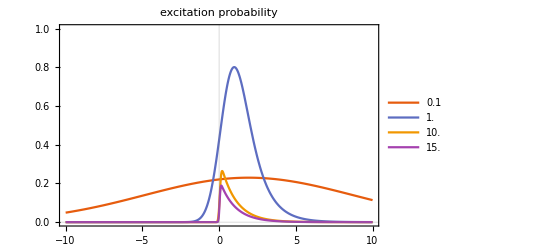

General::munfl: Exp[-5624.54] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12655.2] is too small to represent as a normalized machine number; precision may be lost.

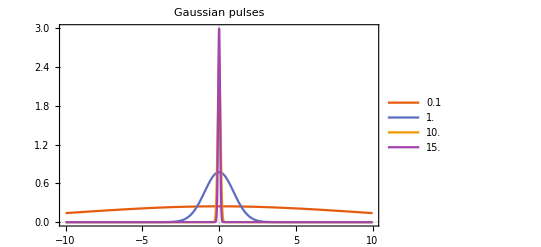

```mathematica
tmin=-100;
tmax=10;
Clear[s,M,b,t]
Γ=1;
Γp=Γ;
Ω0=1.5Γ;
Ωarr={0.1,1,10, 15}Ω0;
PeArr={};
PulseArr={};
For[i=1,i<Length[Ωarr]+1,i++,
Ω=Ωarr[[i]];
g[t]=√Γp(Ω^2/(2π))^(1/4)Exp[-(Ω t)^2/4];
AppendTo[PulseArr, g[t]];
M=({{-Γ, -2g[t], -2g[t]}, {0, -Γ/2, 0}, {0, 0, -Γ/2}});
b=({{-Γ}, {-g[t]}, {-g[t]}});
s=({{s1[t]}, {s2[t]}, {s3[t]}});
eqs=Array[(D[s,t]-(M.s+b))[[#,1]]==0&,3];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,{s1[tmin]==1,s2[tmin]==0,s3[tmin]==0}], s, {t,tmin,tmax}, MaxStepFraction->1/1000]];
Print["Time to run sim step ",i,": ",time];
Pe=1/2(soln[[1,2]]+1);
AppendTo[PeArr,Pe];
]

Plot[PeArr,{t,-10,10},PlotLegends->Ωarr/Ω0,PlotLabel->"excitation probability",PlotRange->{{-10,10},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,-10,10},PlotLegends->Ωarr/Ω0,PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

## simulate Lindblad eq. for Heisenberg operators

Reproduce Fig. 1, but by solving the Linbald equation for the time evolution of the operators and then measuring the expectation values of the operators using <A> = Tr[A(t) ρ] where ρ is fixed in time to be the initial state. Apparently I’ve done this incorrectly, because the results do not agree with the expectation value simulation above.

### solve for expectation values of σz, σ-.

In deriving the equation sdot = M.s + b, matrix elements of the equations for the atomic operators are taken in order to get their expectation values. These expectation values make up the s matrix. In the same fashion, below I have constructed the operator Lindblad equations and taken matrix elements of both sides to pick out the quantities of interest. However, this no longer works-- the equations contain all of the elements of sz and s+, though we have differential equations for only a single element of each, and hence the system is underdetermined. Where is the inconsistency here? Do i need to take the matrix element of each term individually?

```mathematica
sm//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
sz//MatrixForm
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
tmin=-100;
tmax=10;
t0=0;

Γ=1;
Γp=Γ;
Ω0=1.5Γ;
Ωarr={0.1,1,10,15}Ω0;

(*substates kets and density matrices*)
ψatomg={1,0};(*{g,e}*)
ψatome={0,1};(*{g,e}*)
ψfield0={1,0};(*{0,1}*)
ψfield1={0,1};(*{0,1}*)
ρg = Outer[Times,ψatomg,ψatomg];
ρe = Outer[Times,ψatome,ψatome];
ρf0 = Outer[Times,ψfield0,ψfield0];
ρf1= Outer[Times,ψfield1,ψfield1];

(*population projectors*)
"atom g, field 0"
ρ00=KroneckerProduct[ρg,ρf0];
ρ00//MatrixForm
"atom g, field 1"
ρ01=KroneckerProduct[ρg,ρf1];
ρ01//MatrixForm
"atom e, field 0"
ρ10=KroneckerProduct[ρe,ρf0];
ρ10//MatrixForm
"atom e, field 1"
ρ11=KroneckerProduct[ρe,ρf1];
ρ11//MatrixForm

(*initial state*)
ρ0=KroneckerProduct[ρg,ρf1];
```

atom g, field 0

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

atom g, field 1

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

atom e, field 0

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

atom e, field 1

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
(*basis kets*)
ψg0=Flatten@KroneckerProduct[ψatomg,ψfield0];
ψg1=Flatten@KroneckerProduct[ψatomg,ψfield1];
ψe0=Flatten@KroneckerProduct[ψatome,ψfield0];
ψe1=Flatten@KroneckerProduct[ψatome,ψfield1];
```

```mathematica
(*we could also define the projectors with the basis outer products*)
(*Outer[Times,ψg0,ψg0]
Outer[Times,ψg1,ψg1]
Outer[Times,ψe0,ψe0]
Outer[Times,ψe1,ψe1]*)
```

```mathematica
Clear[H,L,t,Sz,Sm,SZ,SM]
SZsolnList={};
SMsolnList={};
PulseArr={};
For[k=1,k<Length[Ωarr]+1,k++,
Ω=Ωarr[[k]];

g=√Γp(Ω^2/(2π))^(1/4)Exp[-(Ω (t-t0))^2/4];
AppendTo[PulseArr, g];

SZinitial={};
SMinitial={};
SZ=Array[Subscript[Sz, #1,#2][t]&,{4,4}];
SM=Array[Subscript[Sm, #1,#2][t]&,{4,4}];

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H=ⅈ g(-ConjugateTranspose[SM].aa+ SM.dag[aa]);

(*decay operator for atom excited state*)
L=√Γ SM;

variables=Join[Flatten@SM,Flatten@SZ];
(*the Heisenberg operators are equivalent to the Schrodinger picture ones at the start time*)
For[i=1,i<5,i++,
For[j=1,j<5,j++,
(*the Heisenberg operators are equivalent to the Schrodinger picture ones at the start time*)
AppendTo[SZinitial,Subscript[Sz, i,j][tmin]==sz[[i,j]]];
];
];
For[i=1,i<5,i++,
For[j=1,j<5,j++,
AppendTo[SMinitial,Subscript[Sm, i,j][tmin]==sm[[i,j]]];
];
];
initialConditions=Join@{SZinitial,SMinitial};

SZdot=ⅈ (H.SZ-SZ.H)+(dag[L].SZ.L-1/2(dag[L].L.SZ+SZ.dag[L].L));
SMdot=ⅈ (H.SM-SM.H)+(dag[L].SM.L-1/2(dag[L].L.SM+SM.dag[L].L));
eqs={
ψg1.D[SZ,t].ψg1==ψg1.SZdot.ψg1,
ψg0.D[SM,t].ψg1==ψg1.SMdot.ψg1
};

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], variables, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",k,": ",time];
AppendTo[SZsolnList,soln[[1]]];
AppendTo[SMsolnList,soln[[2]]];
]
```

NDSolve::underdet: There are more dependent variables, {Sm_(1,1)[t],Sm_(1,2)[t],Sm_(1,3)[t],Sm_(1,4)[t],Sm_(2,1)[t],Sm_(2,2)[t],Sm_(2,3)[t],Sm_(2,4)[t],Sm_(3,1)[t],Sm_(3,2)[t],«22»}, than equations, so the system is underdetermined.

Time to run sim step 1: 0.03125

NDSolve::underdet: There are more dependent variables, {Sm_(1,1)[t],Sm_(1,2)[t],Sm_(1,3)[t],Sm_(1,4)[t],Sm_(2,1)[t],Sm_(2,2)[t],Sm_(2,3)[t],Sm_(2,4)[t],Sm_(3,1)[t],Sm_(3,2)[t],«22»}, than equations, so the system is underdetermined.

Time to run sim step 2: 0.

NDSolve::underdet: There are more dependent variables, {Sm_(1,1)[t],Sm_(1,2)[t],Sm_(1,3)[t],Sm_(1,4)[t],Sm_(2,1)[t],Sm_(2,2)[t],Sm_(2,3)[t],Sm_(2,4)[t],Sm_(3,1)[t],Sm_(3,2)[t],«22»}, than equations, so the system is underdetermined.

General::stop: Further output of NDSolve::underdet will be suppressed during this calculation.

Time to run sim step 3: 0.015625

Time to run sim step 4: 0.

```mathematica
MemberQ[{5Conjugate[Subscript[Sm, 1,2][t]]+2},Subscript[Sm, 1,2][t],Infinity]
```

True

```mathematica
vars={};
For[i=1,i<Length[variables],i++,
If[MemberQ[eqs,variables[[i]],Infinity],AppendTo[vars,variables[[i]]],Print[variables[[i]],"not found"]]
]
vars
```

{Sm_(1,1)[t],Sm_(1,2)[t],Sm_(1,3)[t],Sm_(1,4)[t],Sm_(2,1)[t],Sm_(2,2)[t],Sm_(2,3)[t],Sm_(2,4)[t],Sm_(3,1)[t],Sm_(3,2)[t],Sm_(3,3)[t],Sm_(3,4)[t],Sm_(4,1)[t],Sm_(4,2)[t],Sm_(4,3)[t],Sm_(4,4)[t],Sz_(1,1)[t],Sz_(1,2)[t],Sz_(1,3)[t],Sz_(1,4)[t],Sz_(2,1)[t],Sz_(2,2)[t],Sz_(2,3)[t],Sz_(2,4)[t],Sz_(3,1)[t],Sz_(3,2)[t],Sz_(3,3)[t],Sz_(3,4)[t],Sz_(4,1)[t],Sz_(4,2)[t],Sz_(4,3)[t]}

```mathematica
ψg0.{{z,y,x,w},{z,y,x,w}}
```

### solve for all elements of σ- and σz

I use Sz and Sm to denote the product of σ atomic operators with the field operators. Comparing with the modified optical Bloch equations from Scarani, we can see that only the atomic operators evolve, whereas the field operators have been integrated so that what is left is a static field operator times the time-dependent coupling.

```mathematica
sm//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
sz//MatrixForm
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
tmin=-100;
tmax=10;
t0=0;

Γ=1;
Γp=Γ;
Ω0=1.5Γ;
Ωarr={0.1,1,10,15}Ω0;

(*substates kets and density matrices*)
ψatomg={1,0};(*{g,e}*)
ψatome={0,1};(*{g,e}*)
ψfield0={1,0};(*{0,1}*)
ψfield1={0,1};(*{0,1}*)
ρg = Outer[Times,ψatomg,ψatomg];
ρe = Outer[Times,ψatome,ψatome];
ρf0 = Outer[Times,ψfield0,ψfield0];
ρf1= Outer[Times,ψfield1,ψfield1];

(*population projectors*)
"atom g, field 0"
ρ00=KroneckerProduct[ρg,ρf0];
ρ00//MatrixForm
"atom g, field 1"
ρ01=KroneckerProduct[ρg,ρf1];
ρ01//MatrixForm
"atom e, field 0"
ρ10=KroneckerProduct[ρe,ρf0];
ρ10//MatrixForm
"atom e, field 1"
ρ11=KroneckerProduct[ρe,ρf1];
ρ11//MatrixForm

(*initial state*)
ρ0=KroneckerProduct[ρg,ρf1];
```

atom g, field 0

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

atom g, field 1

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

atom e, field 0

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

atom e, field 1

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
Clear[H,L,t,Sz,Sm,SZ,SM]
SZsolnList={};
SMsolnList={};
PulseArr={};
For[k=1,k<Length[Ωarr]+1,k++,
Ω=Ωarr[[k]];

g=√Γp(Ω^2/(2π))^(1/4)Exp[-(Ω (t-t0))^2/4];
AppendTo[PulseArr, g];

SZinitial={};
SMinitial={};
SZ=Array[Subscript[Sz, #1,#2][t]&,{4,4}];
SM=Array[Subscript[Sm, #1,#2][t]&,{4,4}];

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H=ⅈ g(-ConjugateTranspose[SM].aa+ SM.dag[aa]);

(*decay operator for atom excited state*)
L=√Γ SM;

variables=Join[Flatten@SM,Flatten@SZ];
(*the Heisenberg operators are equivalent to the Schrodinger picture ones at the start time*)
For[i=1,i<5,i++,
For[j=1,j<5,j++,
(*the Heisenberg operators are equivalent to the Schrodinger picture ones at the start time*)
AppendTo[SZinitial,Subscript[Sz, i,j][tmin]==sz[[i,j]]];
];
];
For[i=1,i<5,i++,
For[j=1,j<5,j++,
AppendTo[SMinitial,Subscript[Sm, i,j][tmin]==sm[[i,j]]];
];
];
initialConditions=Join@{SZinitial,SMinitial};

SZdot=ⅈ (H.SZ-SZ.H)+(dag[L].SZ.L-1/2(dag[L].L.SZ+SZ.dag[L].L));
SMdot=ⅈ (H.SM-SM.H)+(dag[L].SM.L-1/2(dag[L].L.SM+SM.dag[L].L));
eqs={};
For[i=1,i<5,i++,
For[j=1,j<5,j++,
AppendTo[eqs,D[Subscript[Sz, i,j][t],t]==SZdot[[i,j]]];
AppendTo[eqs,D[Subscript[Sm, i,j][t],t]==SMdot[[i,j]]];
];
];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], variables, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",k,": ",time];
AppendTo[SZsolnList,ArrayReshape[soln[[17;;]],{4,4}]];
AppendTo[SMsolnList,ArrayReshape[soln[[;;16]],{4,4}]];
]
```

Time to run sim step 1: 0.40625

Time to run sim step 2: 0.4375

Time to run sim step 3: 0.4375

Time to run sim step 4: 0.421875

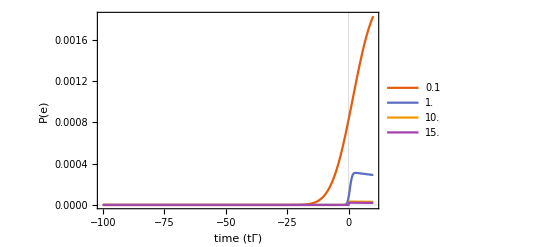

```mathematica
(*this should reproduce the curves of the operator expectation values shown above, but does not*)
ρ=ρ0;
Plot[Evaluate[Array[1/2(Tr[Values[SZsolnList[[#]]].ρ]+1)&,4]],{t,tmin,tmax},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"time (tΓ)","P(e)"},PlotLegends->Ωarr/Ω0]
```

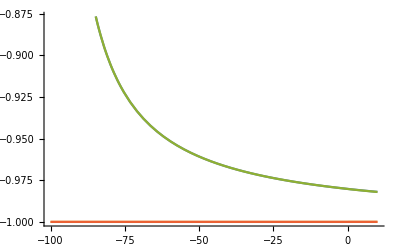

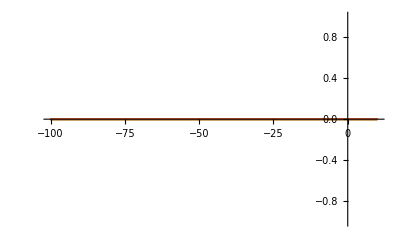

```mathematica
idx=4;
Plot[Evaluate[{Tr[Values[SZsolnList[[idx]]].ρ00],Tr[Values[SZsolnList[[idx]]].ρ01],Tr[Values[SZsolnList[[idx]]].ρ10],Tr[Values[SZsolnList[[idx]]].ρ11]}],{t,tmin,tmax}]
Plot[Evaluate[{Tr[Values[SMsolnList[[idx]]].ρ00],Tr[Values[SMsolnList[[idx]]].ρ01],Tr[Values[SMsolnList[[idx]]].ρ10],Tr[Values[SMsolnList[[idx]]].ρ11]}],{t,tmin,tmax}]
```

```mathematica
Values[SZsolnList[[1]]]//MatrixForm
```

(InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t]
InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t]
InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t]
InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t])

```mathematica
SMinitial
```

{Sm_(1,1)[-100]==0,Sm_(1,2)[-100]==0,Sm_(1,3)[-100]==0,Sm_(1,4)[-100]==0,Sm_(2,1)[-100]==1,Sm_(2,2)[-100]==0,Sm_(2,3)[-100]==0,Sm_(2,4)[-100]==0,Sm_(3,1)[-100]==0,Sm_(3,2)[-100]==0,Sm_(3,3)[-100]==0,Sm_(3,4)[-100]==0,Sm_(4,1)[-100]==0,Sm_(4,2)[-100]==0,Sm_(4,3)[-100]==1,Sm_(4,4)[-100]==0}

```mathematica
SZinitial
```

{Sz_(1,1)[-100]==1,Sz_(1,2)[-100]==0,Sz_(1,3)[-100]==0,Sz_(1,4)[-100]==0,Sz_(2,1)[-100]==0,Sz_(2,2)[-100]==-1,Sz_(2,3)[-100]==0,Sz_(2,4)[-100]==0,Sz_(3,1)[-100]==0,Sz_(3,2)[-100]==0,Sz_(3,3)[-100]==1,Sz_(3,4)[-100]==0,Sz_(4,1)[-100]==0,Sz_(4,2)[-100]==0,Sz_(4,3)[-100]==0,Sz_(4,4)[-100]==-1}

```mathematica
Tr[ρ00.Values[SZsolnList[[1]]]]/.t->tmin//MatrixForm
```

1.

```mathematica
Tr[Values[SZsolnList[[1]]].ρ00]/.t->tmin+1
Tr[Values[SZsolnList[[1]]].ρ00]/.t->tmin+2
Tr[Values[SZsolnList[[1]]].ρ00]/.t->tmin+3
Tr[Values[SZsolnList[[1]]].ρ00]/.t->tmin+4
```

3.49579×10^-8

-0.333333

-0.5

-0.6

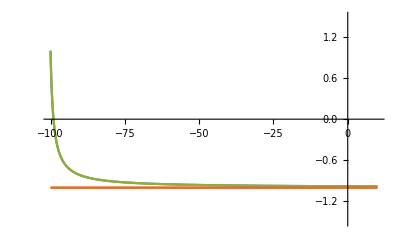

```mathematica
Plot[{Tr[Values[SZsolnList[[1]]].ρ00],Tr[Values[SZsolnList[[1]]].ρ01],Tr[Values[SZsolnList[[1]]].ρ10],Tr[Values[SZsolnList[[1]]].ρ11]},{t,tmin,tmax},PlotRange->{{tmin,tmax},{-1.5,1.5}}]
```

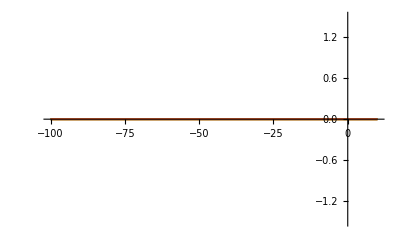

```mathematica
Plot[{Tr[Values[SMsolnList[[1]]].ρ00],Tr[Values[SMsolnList[[1]]].ρ01],Tr[Values[SMsolnList[[1]]].ρ10],Tr[Values[SMsolnList[[1]]].ρ11]},{t,tmin,tmax},PlotRange->{{tmin,tmax},{-1.5,1.5}}]
```

```mathematica
Values[SZsolnList[[1]]].ρ0/.t->0.1//MatrixForm
```

(0 | 0. | 0 | 0
0 | -1. | 0 | 0
0 | -1.93424×10^-15 | 0 | 0
0 | 0. | 0 | 0)

```mathematica
ArrayReshape[{1,2,3,4},{2,2}]
```

{{1,2},{3,4}}

```mathematica
SZsolnList[[]]
```

```mathematica
Tr[ρ00.solnList[[1]]]
```

{Sm_(1,1)[t]->InterpolatingFunction[…][t],Sm_(1,2)[t]->InterpolatingFunction[…][t],Sm_(1,3)[t]->InterpolatingFunction[…][t],Sm_(1,4)[t]->InterpolatingFunction[…][t],Sm_(2,1)[t]->InterpolatingFunction[…][t],Sm_(2,2)[t]->InterpolatingFunction[…][t],Sm_(2,3)[t]->InterpolatingFunction[…][t],Sm_(2,4)[t]->InterpolatingFunction[…][t],Sm_(3,1)[t]->InterpolatingFunction[…][t],Sm_(3,2)[t]->InterpolatingFunction[…][t],Sm_(3,3)[t]->InterpolatingFunction[…][t],Sm_(3,4)[t]->InterpolatingFunction[…][t],Sm_(4,1)[t]->InterpolatingFunction[…][t],Sm_(4,2)[t]->InterpolatingFunction[…][t],Sm_(4,3)[t]->InterpolatingFunction[…][t],Sm_(4,4)[t]->InterpolatingFunction[…][t],Sz_(1,1)[t]->InterpolatingFunction[…][t],Sz_(1,2)[t]->InterpolatingFunction[…][t],Sz_(1,3)[t]->InterpolatingFunction[…][t],Sz_(1,4)[t]->InterpolatingFunction[…][t],Sz_(2,1)[t]->InterpolatingFunction[…][t],Sz_(2,2)[t]->InterpolatingFunction[…][t],Sz_(2,3)[t]->InterpolatingFunction[…][t],Sz_(2,4)[t]->InterpolatingFunction[…][t],Sz_(3,1)[t]->InterpolatingFunction[…][t],Sz_(3,2)[t]->InterpolatingFunction[…][t],Sz_(3,3)[t]->InterpolatingFunction[…][t],Sz_(3,4)[t]->InterpolatingFunction[…][t],Sz_(4,1)[t]->InterpolatingFunction[…][t],Sz_(4,2)[t]->InterpolatingFunction[…][t],Sz_(4,3)[t]->InterpolatingFunction[…][t],Sz_(4,4)[t]->InterpolatingFunction[…][t]}

```mathematica
SZ//MatrixForm
```

(Sz_(1,1)[t] | Sz_(1,2)[t] | Sz_(1,3)[t] | Sz_(1,4)[t]
Sz_(2,1)[t] | Sz_(2,2)[t] | Sz_(2,3)[t] | Sz_(2,4)[t]
Sz_(3,1)[t] | Sz_(3,2)[t] | Sz_(3,3)[t] | Sz_(3,4)[t]
Sz_(4,1)[t] | Sz_(4,2)[t] | Sz_(4,3)[t] | Sz_(4,4)[t])

```mathematica
variables
```

{Sm_(1,1)[t],Sm_(1,2)[t],Sm_(1,3)[t],Sm_(1,4)[t],Sm_(2,1)[t],Sm_(2,2)[t],Sm_(2,3)[t],Sm_(2,4)[t],Sm_(3,1)[t],Sm_(3,2)[t],Sm_(3,3)[t],Sm_(3,4)[t],Sm_(4,1)[t],Sm_(4,2)[t],Sm_(4,3)[t],Sm_(4,4)[t],Sm_(1,1)[t],Sm_(1,2)[t],Sm_(1,3)[t],Sm_(1,4)[t],Sm_(2,1)[t],Sm_(2,2)[t],Sm_(2,3)[t],Sm_(2,4)[t],Sm_(3,1)[t],Sm_(3,2)[t],Sm_(3,3)[t],Sm_(3,4)[t],Sm_(4,1)[t],Sm_(4,2)[t],Sm_(4,3)[t],Sm_(4,4)[t]}

### testing - compare ρ eqs with s eqs

```mathematica
M=({{-Γ, -2g, -2g}, {0, -Γ/2, 0}, {0, 0, -Γ/2}});
b=({{-Γ}, {-g}, {-g}});
s=({{s1}, {s2}, {s3}});
s0=({{1}, {0}, {0}});
M.s+b//MatrixForm
```

(-2 g s2-2 g s3-Γ-s1 Γ
-g-(s2 Γ)/2
-g-(s3 Γ)/2)

```mathematica
H=I g(-sp.aa+ sm.dag[aa]);
L=√Γ sm;

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, L, tmin];
Refine[eqs,Γ>0]//Simplify//MatrixForm//TraditionalForm
```

(Γ ρ_(1,1)(t)+ρ_(1,1)'(t)==0
Γ ρ_(1,2)(t)+2 ρ_(1,2)'(t)==2 g ρ_(1,3)(t)
g ρ_(1,2)(t)+Γ ρ_(1,3)(t)+ρ_(1,3)'(t)==0
Γ ρ_(1,4)(t)+2 ρ_(1,4)'(t)==0
g Conjugate[ρ_(2,3)(t)]+g ρ_(2,3)(t)+Γ ρ_(1,1)(t)==ρ_(2,2)'(t)
g ρ_(2,2)(t)+1/2 Γ ρ_(2,3)(t)+ρ_(2,3)'(t)==g ρ_(3,3)(t)
g ρ_(3,4)(t)+Γ ρ_(1,3)(t)==ρ_(2,4)'(t)
g Conjugate[ρ_(2,3)(t)]+g ρ_(2,3)(t)+Γ ρ_(3,3)(t)+ρ_(3,3)'(t)==0
2 g ρ_(2,4)(t)+Γ ρ_(3,4)(t)+2 ρ_(3,4)'(t)==0
Γ ρ_(3,3)(t)==ρ_(4,4)'(t))

## simulate Lindblad density matrix eq.

Reproduce Fig. 1, but by solving the density matrix equation.  For high-bandwidth (temporally short) pulses, this agrees with the simulation of the s state from the Heisenberg-Langevin equations above, but they do not agree for longer duration pulses.  With no free energy terms for the field and the atom, the interaction and Schrodinger pictures coincide. However, perhaps I need to account for the energies, since the states are not all degenerate even at zero detuning: atom in g and field in 0 is not degenerate with atom in e, field in 0, and so on.

### ignore free energy of the atom, field

In this case, the interaction and Schrodinger picture Hamiltonians and states coincide.

```mathematica
tmin=-100;
tmax=10;
t0=0;
(*tmin=0;
tmax=110;
t0=100;*) (*the photon envelope is centered at t0*)

Γ=1;
Γp=Γ;
Ω0=1.5Γ;
Ωarr={0.1,1,10,15}Ω0;

(*basis kets*)
ψatomgfield0=Outer[Times,{1,0},{1,0}];
ψatomgfield1=Outer[Times,{1,0},{0,1}];
ψatomefield0=Outer[Times,{0,1},{1,0}];
ψatomefield1=Outer[Times,{0,1},{0,1}];

(*initial substates, assuming product state input*)
ψ0atom={1,0};(*{g,e}*)
ψ0field={0,1};(*{0,1}*)
ρ0atom=Outer[Times,ψ0atom,ψ0atom];
ρ0field=Outer[Times,ψ0field,ψ0field];
ρ0=KroneckerProduct[ρ0atom,ρ0field];
ρ0//MatrixForm
(*field starts in N=1 state, atom in g*)
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Time to run sim step 1: 0.046875

Time to run sim step 2: 0.046875

Time to run sim step 3: 0.0625

Time to run sim step 4: 0.046875

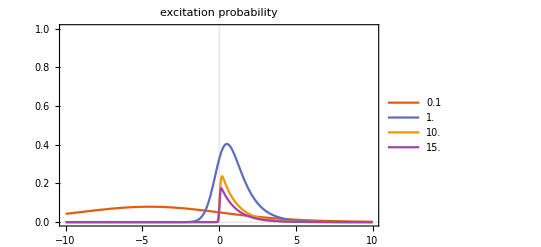

General::munfl: Exp[-5624.54] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12655.2] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
Clear[H,L,t,ρ,rho]
PeArr={};
PulseArr={};
For[i=1,i<Length[Ωarr]+1,i++,
Ω=Ωarr[[i]];

g=√Γp(Ω^2/(2π))^(1/4)Exp[-(Ω (t-t0))^2/4];
AppendTo[PulseArr, g];

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H=I g(-sp.aa+ sm.dag[aa]);

(*decay operator for atom excited state*)
L=√Γ sm;(*decay and absorption*)

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, {L}, tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
Pe=soln[[popIdcs[[3]],2]];
AppendTo[PeArr,Pe];
]

Plot[PeArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax-t0),tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

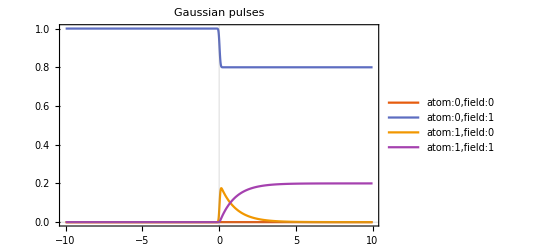

```mathematica
Plot[Evaluate[Array[soln[[popIdcs[[#]],2]]&,4]],{t,tmax-2(tmax-t0),tmax},PlotLegends->{"atom:0,field:0","atom:0,field:1","atom:1,field:0","atom:1,field:1"},PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

```mathematica
L//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
{evals,evecs}=Eigensystem[L]
```

{{0,0,0,0},{{0,0,0,1},{0,1,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
Transpose[evecs]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
Transpose[evecs].L.evecs//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
initialConditions
```

{ρ_(1,1)[-100]==0,ρ_(1,2)[-100]==0,ρ_(1,3)[-100]==0,ρ_(1,4)[-100]==0,ρ_(2,2)[-100]==1,ρ_(2,3)[-100]==0,ρ_(2,4)[-100]==0,ρ_(3,3)[-100]==0,ρ_(3,4)[-100]==0,ρ_(4,4)[-100]==0}

```mathematica
H//MatrixForm
```

(0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | (0. +2.99603 I) E^(-126.563 t^2) | 0. +0. I
0. +0. I | (0. -2.99603 I) E^(-126.563 t^2) | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I)

```mathematica
sm//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

### account for free energy of the atom, field

In this case, the interaction and Schrodinger picture Hamiltonians are different up to a unitary transformation U = e^(IH_0 t/ℏ) where H0 is the Hamiltonian which contains the energies of the system. This does not change the simulation results that I obtain.

```mathematica
tmin=-100;
tmax=10;
t0=0
(*tmin=0;
tmax=110;
t0=100;*) (*the photon envelope is centered at t0*)

Γ=1;
Γp=Γ;
Ω0=1.5Γ;
Ωarr={0.1,1,10,15}Ω0;

(*basis kets*)
ψatomgfield0=Outer[Times,{1,0},{1,0}];
ψatomgfield1=Outer[Times,{1,0},{0,1}];
ψatomefield0=Outer[Times,{0,1},{1,0}];
ψatomefield1=Outer[Times,{0,1},{0,1}];

(*initial substates, assuming product state input*)
ψ0atom={1,0};(*{g,e}*)
ψ0field={0,1};(*{0,1}*)
ρ0atom=Outer[Times,ψ0atom,ψ0atom];
ρ0field=Outer[Times,ψ0field,ψ0field];
ρ0=KroneckerProduct[ρ0atom,ρ0field];
ρ0//MatrixForm
(*field starts in N=1 state, atom in g*)
```

0

```mathematica
E^(I H0 t)HI E^(-I H0 t)//MatrixForm
```

(0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | (0. +2.99603 I) E^(-126.563 t^2) | 0. +0. I
0. +0. I | (0. -2.99603 I) E^(-126.563 t^2) | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I)

```mathematica
HI//MatrixForm
```

(0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | (0. +2.99603 I) E^(-126.563 t^2) | 0. +0. I
0. +0. I | (0. -2.99603 I) E^(-126.563 t^2) | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I)

```mathematica
Clear[ωa,ωf]
Hatom=ωa/2 σz;
Hfield=ωf/2 σz;
Hatomfield=KroneckerProduct[Hatom,σ0]+KroneckerProduct[σ0,Hfield];
Hatomfield//MatrixForm
ωa=1;
ωf=1;
```

(ωa/2+ωf/2 | 0 | 0 | 0
0 | ωa/2-ωf/2 | 0 | 0
0 | 0 | -ωa/2+ωf/2 | 0
0 | 0 | 0 | -ωa/2-ωf/2)

```mathematica
Clear[H,L,t,ρ,rho]
PeArr={};
PulseArr={};
For[i=1,i<Length[Ωarr]+1,i++,
Ω=Ωarr[[i]];

g=√Γp(Ω^2/(2π))^(1/4)Exp[-(Ω (t-t0))^2/4];
AppendTo[PulseArr, g];

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H0=Hatomfield;
HI=I g(-sp.aa+ sm.dag[aa]);
H=H0+HI;

(*decay operator for atom excited state*)
L=√Γ sm;

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, {L}, tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
Pe=soln[[popIdcs[[3]],2]];
AppendTo[PeArr,Pe];
]

Plot[PeArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax-t0),tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

Time to run sim step  1 :  0.0625

Time to run sim step  2 :  0.046875

Time to run sim step  3 :  0.078125

Time to run sim step  4 :  0.046875

-Graphics-

General::munfl: Exp[-5624.54] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12655.2] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
Plot[Evaluate[Array[soln[[popIdcs[[#]],2]]&,4]],{t,tmax-2(tmax-t0),tmax},PlotLegends->{"atom:0,field:0","atom:0,field:1","atom:1,field:0","atom:1,field:1"},PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
H//MatrixForm
```

(1. +0. I | 0. +0. I | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | (0. +2.99603 I) E^(-126.563 t^2) | 0. +0. I
0. +0. I | (0. -2.99603 I) E^(-126.563 t^2) | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | 0. +0. I | -1.+0. I)

```mathematica
ρcollapse
```

{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}}

```mathematica
L//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
{evals,evecs}=Eigensystem[L]
```

{{0,0,0,0},{{0,0,0,1},{0,1,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
Transpose[evecs]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
Transpose[evecs].L.evecs//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
initialConditions
```

{ρ_(1,1)[-100]==0,ρ_(1,2)[-100]==0,ρ_(1,3)[-100]==0,ρ_(1,4)[-100]==0,ρ_(2,2)[-100]==1,ρ_(2,3)[-100]==0,ρ_(2,4)[-100]==0,ρ_(3,3)[-100]==0,ρ_(3,4)[-100]==0,ρ_(4,4)[-100]==0}

```mathematica
H//MatrixForm
```

(0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | (0. +2.99603 I) E^(-126.563 t^2) | 0. +0. I
0. +0. I | (0. -2.99603 I) E^(-126.563 t^2) | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I)

```mathematica
sm//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

### testing - compare ρ eqs with s eqs

```mathematica
M=({{-Γ, -2g, -2g}, {0, -Γ/2, 0}, {0, 0, -Γ/2}});
b=({{-Γ}, {-g}, {-g}});
s=({{s1}, {s2}, {s3}});
s0=({{1}, {0}, {0}});
M.s+b//MatrixForm
```

(-2 g s2-2 g s3-Γ-s1 Γ
-g-(s2 Γ)/2
-g-(s3 Γ)/2)

```mathematica
H=I g(-sp.aa+ sm.dag[aa]);
L=√Γ sm;

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, L, tmin];
Refine[eqs,Γ>0]//Simplify//MatrixForm//TraditionalForm
```

(Γ ρ_(1,1)(t)+ρ_(1,1)'(t)==0
Γ ρ_(1,2)(t)+2 ρ_(1,2)'(t)==2 g ρ_(1,3)(t)
g ρ_(1,2)(t)+Γ ρ_(1,3)(t)+ρ_(1,3)'(t)==0
Γ ρ_(1,4)(t)+2 ρ_(1,4)'(t)==0
g Conjugate[ρ_(2,3)(t)]+g ρ_(2,3)(t)+Γ ρ_(1,1)(t)==ρ_(2,2)'(t)
g ρ_(2,2)(t)+1/2 Γ ρ_(2,3)(t)+ρ_(2,3)'(t)==g ρ_(3,3)(t)
g ρ_(3,4)(t)+Γ ρ_(1,3)(t)==ρ_(2,4)'(t)
g Conjugate[ρ_(2,3)(t)]+g ρ_(2,3)(t)+Γ ρ_(3,3)(t)+ρ_(3,3)'(t)==0
2 g ρ_(2,4)(t)+Γ ρ_(3,4)(t)+2 ρ_(3,4)'(t)==0
Γ ρ_(3,3)(t)==ρ_(4,4)'(t))

8 lines of corrupt data deleted.

### Hamiltonian + Lindblad from input-output theory - correct

See “Quantum interactions with pulses of radiation” by Kiilerich and Molmer. It’s not clear that I’m correctly applying their theory, since input-output theory and cascaded systems as they discuss are “uni-directional”. In Scarani, a fraction of the atomic decay goes back into the pulse mode, while in input-output theory, the outgoing pulse mode would have its own set of operators and I would have to reformulate the problem slightly. In any case, the results here are closer to the Scarani result.

#### account for input mode only

This is very close! It only disagrees with Scarani for the bandwidth Ω>>Γ, which is unlikely to be true for the theory of interest. Todo: reproduce Pe plots for other choices of pulse shapes.

```mathematica
(*basis kets*)
ψatomgfield0=Outer[Times,{1,0},{1,0}];
ψatomgfield1=Outer[Times,{1,0},{0,1}];
ψatomefield0=Outer[Times,{0,1},{1,0}];
ψatomefield1=Outer[Times,{0,1},{0,1}];

(*initial substates, assuming product state input*)
ψ0atom={1,0};(*{g,e}*)
ψ0field={0,1};(*{0,1}*)
ρ0atom=Outer[Times,ψ0atom,ψ0atom];
ρ0field=Outer[Times,ψ0field,ψ0field];
ρ0=KroneckerProduct[ρ0atom,ρ0field];
ρ0//MatrixForm
(*field starts in N=1 state, atom in g*)
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[Ω,t0]
(*Integrate[Exp[-(Ω (t-t0))^2/4]^2,{t,0,t}]*)
Integrate[Exp[-(Ω (t-t0))^2/4]^2,{t,-∞,t}]
```

ConditionalExpression[(√(π/2) (Ω+√(Ω^2) Erf[((t-t0) Ω)/(√2)]))/(Ω √(Ω^2)), Re[Ω^2]≥0]

```mathematica
(√(π/2) (Ω+√(Ω^2) Erf[((t-t0) Ω)/(√2)]))/(Ω √(Ω^2))
```

Time to run sim step 1: 0.046875

Time to run sim step 2: 0.046875

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {10} at {t,ρ_(1,1)[t],ρ_(1,2)[t],ρ_(1,3)[t],ρ_(1,4)[t],ρ_(2,2)[t],ρ_(2,3)[t],ρ_(2,4)[t],ρ_(3,3)[t],ρ_(3,4)[t],«1»} = {0.55327,0.,0.,0.,0.,7.42321×10^-11,-2.50711×10^-9,0.,0.192625,0.,«1»}.

Time to run sim step 3: 0.046875

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {10} at {t,ρ_(1,1)[t],ρ_(1,2)[t],ρ_(1,3)[t],ρ_(1,4)[t],ρ_(2,2)[t],ρ_(2,3)[t],ρ_(2,4)[t],ρ_(3,3)[t],ρ_(3,4)[t],«1»} = {0.3728,0.,0.,0.,0.,2.29427×10^-9,2.93848×10^-9,0.,0.153625,0.,«1»}.

Time to run sim step 4: 0.046875

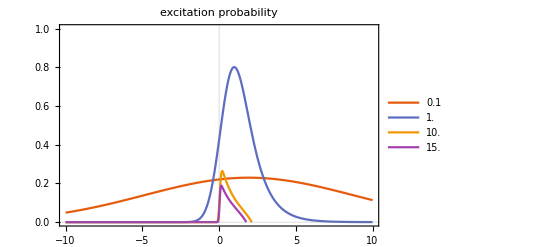

General::munfl: Exp[-5624.54] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12655.2] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
Γ=1;
Γp=Γ;
Ω0=1.5Γ;

tmin=-100;
tmax=10;
t0=0;

Ωarr={0.1,1,10,15}Ω0;
Clear[H,L,t,ρ,rho]
PeArr={};
PulseArr={};
For[i=1,i<Length[Ωarr]+1,i++,
Ω=Ωarr[[i]];

(*u=(Ω^2/(2π))^(1/4)Exp[-(Ω (t-t0))^2/4];(*pulse envelope*)
gu=u/(√(1-(Ω^2/(2π))^(1/2)(√(π/2) (Erf[((t-t0) Ω)/(√2)]+Erf[(t0 Ω)/(√2)]))/Ω));*)
u=(Ω^2/(2π))^(1/4)Exp[-(Ω (t-t0))^2/4];
gu=u/(√(1-(Ω^2/(2π))^(1/2)(√(π/2) (Ω+√(Ω^2) Erf[((t-t0) Ω)/(√2)]))/(Ω √(Ω^2))));
(*gu=(Ω^2/(2π))^(1/4)Exp[-(Ω (t-t0))^2/4];*)

AppendTo[PulseArr, u];

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H=I(√Γ)/2 gu(sm.dag[aa]-sp.aa);(*eq 8. our decay rate is already included in g*)

(*decay operator for atom excited state*)
L=√Γ sm + gu aa;(*decay and absorption*)

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, {L}, tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
Pe=soln[[popIdcs[[3]],2]];
AppendTo[PeArr,Pe];
]

Plot[PeArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax-t0),tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

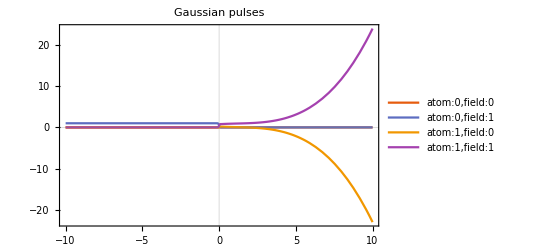

```mathematica
Plot[Evaluate[Array[soln[[popIdcs[[#]],2]]&,4]],{t,tmax-2(tmax-t0),tmax},PlotLegends->{"atom:0,field:0","atom:0,field:1","atom:1,field:0","atom:1,field:1"},PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

```mathematica
L//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
{evals,evecs}=Eigensystem[L]
```

{{0,0,0,0},{{0,0,0,1},{0,1,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
Transpose[evecs]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
Transpose[evecs].L.evecs//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
initialConditions
```

{ρ_(1,1)[-100]==0,ρ_(1,2)[-100]==0,ρ_(1,3)[-100]==0,ρ_(1,4)[-100]==0,ρ_(2,2)[-100]==1,ρ_(2,3)[-100]==0,ρ_(2,4)[-100]==0,ρ_(3,3)[-100]==0,ρ_(3,4)[-100]==0,ρ_(4,4)[-100]==0}

```mathematica
H//MatrixForm
```

(0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | (0. +2.99603 I) E^(-126.563 t^2) | 0. +0. I
0. +0. I | (0. -2.99603 I) E^(-126.563 t^2) | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I)

```mathematica
sm//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

#### naively equate output mode to input mode

Doesn’t match Scarani. I’m cheating and naively saying the input and output modes are the same. Seems like if we are merely book-keeping by having different modes there shouldn’t be a problem with this approach.

```mathematica
(*initial substates, assuming product state input*)
ψ0atom={1,0};(*{g,e}*)
ψ0field={0,1};(*{0,1}*)
ρ0atom=Outer[Times,ψ0atom,ψ0atom];
ρ0field=Outer[Times,ψ0field,ψ0field];
ρ0=KroneckerProduct[ρ0atom,ρ0field];
ρ0//MatrixForm
(*field starts in N=1 state, atom in g*)
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[Ω,t0,u,decay]
Integrate[Exp[-(Ω (t-t0))^2/4]^2,{t,0,t}]
```

(√(π/2) (Erf[((t-t0) Ω)/(√2)]+Erf[(t0 Ω)/(√2)]))/Ω

```mathematica
(*input pulse mode*)
u[t_]=(Ω^2/(2π))^(1/4)Exp[-(Ω (t-t0))^2/4];
decay[t_]=Piecewise[{{0,t<0},{Exp[-t/2],t>=0}}];(*Gamma=1*)
(*assume output pulse is exponential convolved with Gaussian*)
v=Assuming[Ω>0&&t∈Reals&&t0>0,Integrate[u[y]decay[t-y],{y,-∞,∞}]]
```

1/(√Ω)ⅇ^(-t/2+t0/2+1/(4 Ω^2)) (π/2)^(1/4) (1-Sign[-t+t0+1/Ω^2]+Erfc[Abs[1+(-t+t0) Ω^2]/(2 Ω)] Sign[-t+t0+1/Ω^2])

```mathematica
Assuming[Ω>0&&t∈Reals&&t0>0,Integrate[v^2,{t,0,∞}]]
```

∫_0^∞ 1/Ω ⅇ^(-t+t0+1/(2 Ω^2)) √(π/2) (1-Sign[-t+t0+1/Ω^2]+Erfc[Abs[1+(-t+t0) Ω^2]/(2 Ω)] Sign[-t+t0+1/Ω^2])^2ⅆt

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == -100..

Time to run sim step 1: 0.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == -100..

Time to run sim step 2: 0.015625

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == -100..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

Time to run sim step 3: 0.

Time to run sim step 4: 0.

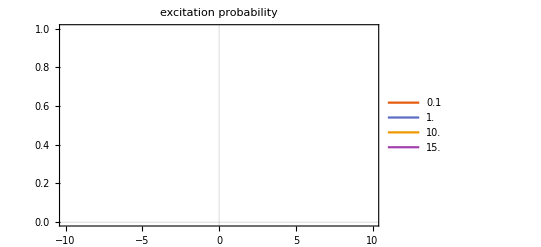

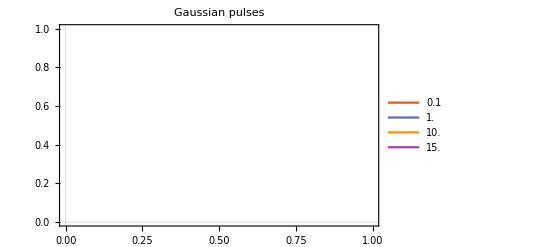

```mathematica
Γ=1;
Γp=Γ;
Ω0=1.5Γ;

tmin=-100;
tmax=10;
t0=0;

Ωarr={0.1,1,10,15}Ω0;
Clear[H,L,t,ρ,rho]
PeArr={};
PulseArr={};
For[i=1,i<Length[Ωarr]+1,i++,
Ω=Ωarr[[i]];


(*temporal mode in a cavity that leaks mode into temporal mode u*)
gu=u/(√(1-(Ω^2/(2π))^(1/2)(√(π/2) (Erf[((t-t0) Ω)/(√2)]+Erf[(t0 Ω)/(√2)]))/Ω));
(*temporal mode in a cavity that absorbs mode from temporal mode u*)
gv=u/(√((2^(3/4) π^(1/4) (Erf[1/(2 Ω)]+Erf[(t0 Ω)/2]+Erfc[1/(2 Ω)]+ⅇ^(t0/2+1/(4 Ω^2)) Erfc[(1+t0 Ω^2)/(2 Ω)]))/(√Ω)));
(*(*naively assume the temporal mode is just the one we want, ignoring the virtual cavities -- doesn't work*)
gu=gv=(Ω^2/(2π))^(1/4)Exp[-(Ω (t-t0))^2/4];*)

AppendTo[PulseArr, gu];

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H=I/2(√Γ gu sm.dag[aa]+√Γ gv sp.aa+gu gv dag[aa].aa-(√Γ gu sp.aa+√Γ gv sm.dag[aa]+gu gv aa.dag[aa]));(*eq 8. our decay rate is already included in g*)

L=√Γ sm + gu aa+ gu aa;

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, {L}, tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
Pe=soln[[popIdcs[[3]],2]];
AppendTo[PeArr,Pe];
]

Plot[PeArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax-t0),tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

```mathematica
Plot[Evaluate[Array[soln[[popIdcs[[#]],2]]&,4]],{t,tmax-2(tmax-t0),tmax},PlotLegends->{"atom:0,field:0","atom:0,field:1","atom:1,field:0","atom:1,field:1"},PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
L//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
{evals,evecs}=Eigensystem[L]
```

{{0,0,0,0},{{0,0,0,1},{0,1,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
Transpose[evecs]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
Transpose[evecs].L.evecs//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
initialConditions
```

{ρ_(1,1)[-100]==0,ρ_(1,2)[-100]==0,ρ_(1,3)[-100]==0,ρ_(1,4)[-100]==0,ρ_(2,2)[-100]==1,ρ_(2,3)[-100]==0,ρ_(2,4)[-100]==0,ρ_(3,3)[-100]==0,ρ_(3,4)[-100]==0,ρ_(4,4)[-100]==0}

```mathematica
H//MatrixForm
```

(0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | (0. +2.99603 I) E^(-126.563 t^2) | 0. +0. I
0. +0. I | (0. -2.99603 I) E^(-126.563 t^2) | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I)

```mathematica
sm//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

### compare input-output theory and H.-L. for various pulse shapes - correct

#### define pulse shapes and simulation parameters

```mathematica
Clear[Ω];
gaussian=(Ω^2/(2π))^(1/4)Exp[-(Ω t)^2/4];sech=√(Ω/2)Sech[Ω t];
rect=Piecewise[{{√(Ω/2),0<=t<=2/Ω},{0,t>2/Ω}}];
symm=√Ω Exp[-Ω Abs[t]];
decay=Piecewise[{{√Ω Exp[-Ω t/2],t>0}}];
rising=Piecewise[{{√Ω Exp[Ω t/2],t<0}}];
PulseArr={gaussian,sech,rect,symm,decay,rising};
PulseLegend={"Gaussian", "Hyperbolic secant", "Rect", "Symm. exponential", "Decaying exponential", "Rising exponential"};
Γ=1;
Γp=Γ;
Ω0=1.5Γ;

tmin=-100;
tmax=10;

Ω=Ω0;
```

#### Lindblad eq for various pulse shapes

```mathematica
(*basis kets*)
ψatomgfield0=Outer[Times,{1,0},{1,0}];
ψatomgfield1=Outer[Times,{1,0},{0,1}];
ψatomefield0=Outer[Times,{0,1},{1,0}];
ψatomefield1=Outer[Times,{0,1},{0,1}];

(*initial substates, assuming product state input*)
ψ0atom={1,0};(*{g,e}*)
ψ0field={0,1};(*{0,1}*)
ρ0atom=Outer[Times,ψ0atom,ψ0atom];
ρ0field=Outer[Times,ψ0field,ψ0field];
ρ0=KroneckerProduct[ρ0atom,ρ0field];
ρ0//MatrixForm
(*field starts in N=1 state, atom in g*)
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[H,L,t,ρ,rho]
PeLindbladArr={};

For[i=1,i<Length[PulseArr]+1,i++,
u=PulseArr[[i]];
uSquaredIntegral=Assuming[t∈Reals,Integrate[u^2/.t->τ,{τ,-∞,t}]];
gu=u/(√(1-uSquaredIntegral));

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H=I(√Γ)/2 gu(sm.dag[aa]-sp.aa);(*eq 8. our decay rate is already included in g*)

(*decay operator for atom excited state*)
L=√Γ sm + gu aa;(*decay and absorption*)

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, {L}, tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
Pe=soln[[popIdcs[[3]],2]];
AppendTo[PeLindbladArr,Pe];
]
```

Time to run sim step 1: 0.0625

Time to run sim step 2: 0.0625

NDSolve::ndsz: At t == 1.33333, step size is effectively zero; singularity or stiff system suspected.

Time to run sim step 3: 0.234375

Time to run sim step 4: 0.0625

Time to run sim step 5: 0.078125

Time to run sim step 6: 0.0625

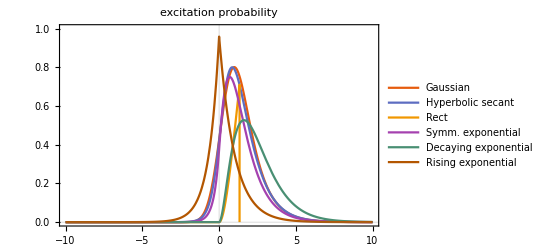

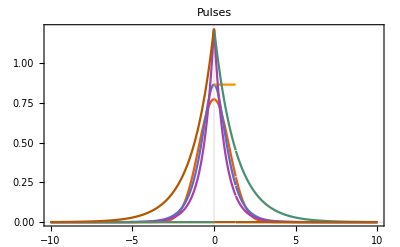

```mathematica
Plot[PeLindbladArr,{t,tmax-2tmax,tmax},PlotLegends->PulseLegend,PlotLabel->"excitation probability",PlotRange->{{tmax-2tmax,tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2tmax,tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"Pulses",PlotRange->All,PlotTheme->"Scientific"]
```

#### Heisenberg-Langevin eqs for various pulse shapes

```mathematica
Clear[s,M,b,t]
PeHLArr={};
For[i=1,i<Length[PulseArr]+1,i++,
g=PulseArr[[i]];
M=({{-Γ, -2g, -2g}, {0, -Γ/2, 0}, {0, 0, -Γ/2}});
b=({{-Γ}, {-g}, {-g}});
s=({{s1[t]}, {s2[t]}, {s3[t]}});
eqs=Array[(D[s,t]-(M.s+b))[[#,1]]==0&,3];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,{s1[tmin]==1,s2[tmin]==0,s3[tmin]==0}], s, {t,tmin,tmax}, MaxStepFraction->1/1000]];
Print["Time to run sim step ",i,": ",time];
Pe=1/2(soln[[1,2]]+1);
AppendTo[PeHLArr,Pe];
]
```

Time to run sim step 1: 0.

Time to run sim step 2: 0.

Time to run sim step 3: 0.015625

Time to run sim step 4: 0.015625

Time to run sim step 5: 0.

Time to run sim step 6: 0.

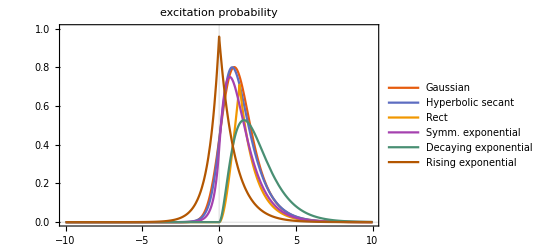

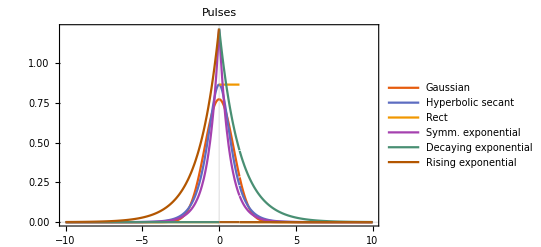

```mathematica
Plot[PeHLArr,{t,tmax-2(tmax),tmax},PlotLegends->PulseLegend,PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax),tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2(tmax),tmax},PlotLegends->PulseLegend,PlotLabel->"Pulses",PlotRange->All,PlotTheme->"Scientific"]
```

#### Compare the solutions from the two methods

The plot below shows that the input-output theory Lindblad equation and Heisenberg-Langevin equations agree for all pulse shapes, except where t>2/Ω for the rectangular pulse, which is because Mathematica didn’t properly integrate it in the calculation of g(t).

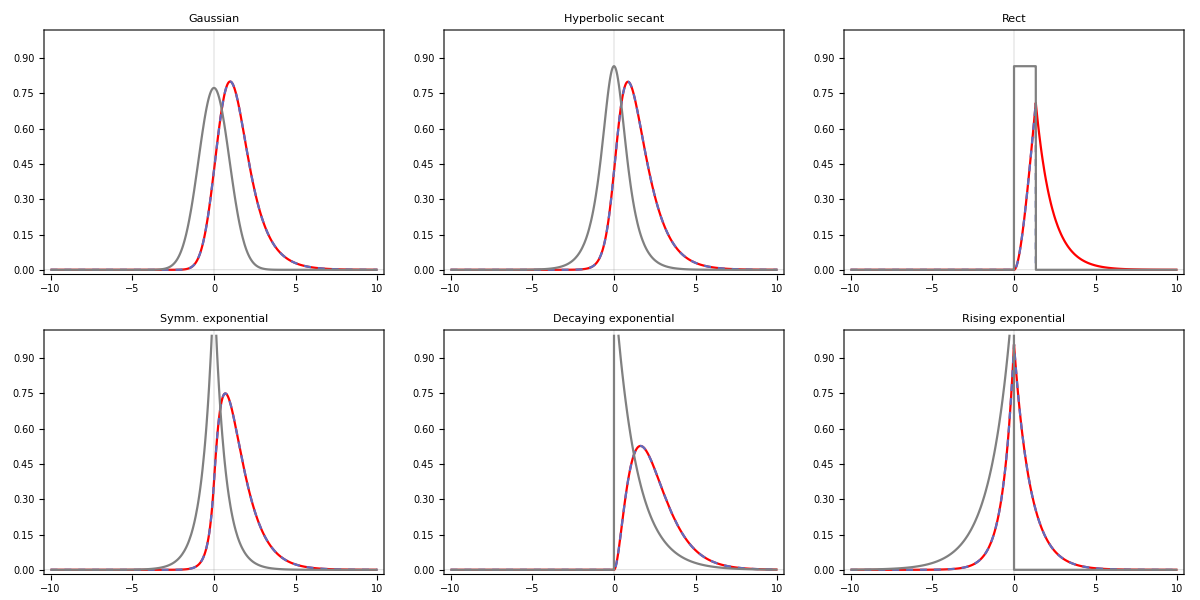

```mathematica
Grid[ArrayReshape[Table[Plot[{PeHLArr[[j]],PeLindbladArr[[j]],PulseArr[[j]]},{t,tmax-2(tmax),tmax},PlotLabel->PulseLegend[[j]],PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax),tmax},{0,1}},PlotTheme->"Scientific",PlotStyle->{Red,Dashed,Gray}],{j,Range[Length[PulseArr]]}],{2,3}]]
```

### compare input-output theory and H.-L. for different coupling strengths - correct

#### define different coupling strengths and simulation parameters

```mathematica
Clear[Ω];
gaussian=(Ω^2/(2π))^(1/4)Exp[-(Ω t)^2/4];sech=√(Ω/2)Sech[Ω t];
rect=Piecewise[{{√(Ω/2),0<=t<=2/Ω},{0,t>2/Ω}}];
symm=√Ω Exp[-Ω Abs[t]];
decay=Piecewise[{{√Ω Exp[-Ω t/2],t>0}}];
rising=Piecewise[{{√Ω Exp[Ω t/2],t<0}}];
(*PulseArr={gaussian,sech,rect,symm,decay,rising};
PulseLegend={"Gaussian", "Hyperbolic secant", "Rect", "Symm. exponential", "Decaying exponential", "Rising exponential"};*)

pulse =gaussian;

Γ=1;
ΓpArr={0.1, 0.5,1}Γ;
Ω0=1.5Γ;

tmin=-100;
tmax=10;

Ω=Ω0;
```

#### Lindblad eq for different coupling strengths

```mathematica
(*basis kets*)
ψatomgfield0=Outer[Times,{1,0},{1,0}];
ψatomgfield1=Outer[Times,{1,0},{0,1}];
ψatomefield0=Outer[Times,{0,1},{1,0}];
ψatomefield1=Outer[Times,{0,1},{0,1}];

(*initial substates, assuming product state input*)
ψ0atom={1,0};(*{g,e}*)
ψ0field={0,1};(*{0,1}*)
ρ0atom=Outer[Times,ψ0atom,ψ0atom];
ρ0field=Outer[Times,ψ0field,ψ0field];
ρ0=KroneckerProduct[ρ0atom,ρ0field];
ρ0//MatrixForm
(*field starts in N=1 state, atom in g*)
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[H,L,t,ρ,rho]
PeLindbladArr={};

PulseArr={};
For[i=1,i<Length[ΓpArr]+1,i++,
u=ΓpArr[[i]]pulse;
AppendTo[PulseArr,u];
uSquaredIntegral=Assuming[t∈Reals,Integrate[u^2/.t->τ,{τ,-∞,t}]];
gu=u/(√(1-uSquaredIntegral));

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H=I(√Γ)/2 gu(sm.dag[aa]-sp.aa);(*eq 8. our decay rate is already included in g*)

(*decay operator for atom excited state*)
L=√Γ sm + gu aa;(*decay and absorption*)

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, {L}, tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
Pe=soln[[popIdcs[[3]],2]];
AppendTo[PeLindbladArr,Pe];
]
```

Time to run sim step 1: 0.0625

Time to run sim step 2: 0.078125

Time to run sim step 3: 0.0625

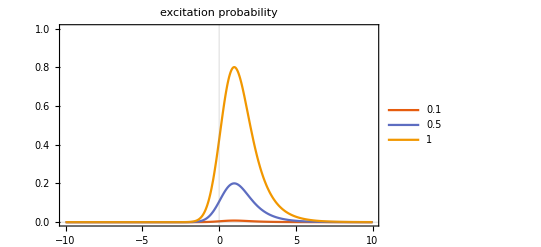

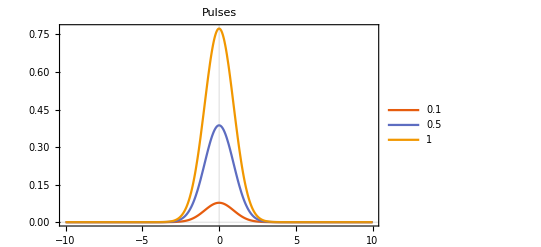

```mathematica
Plot[PeLindbladArr,{t,tmax-2tmax,tmax},PlotLegends->ΓpArr/Γ,PlotLabel->"excitation probability",PlotRange->{{tmax-2tmax,tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2tmax,tmax},PlotLegends->ΓpArr/Γ,PlotLabel->"Pulses",PlotRange->All,PlotTheme->"Scientific"]
```

#### Heisenberg-Langevin eqs for different coupling strengths

```mathematica
Clear[s,M,b,t]
PeHLArr={};
PulseArr={};
For[i=1,i<Length[ΓpArr]+1,i++,
g=ΓpArr[[i]]pulse;
AppendTo[PulseArr,g];

M=({{-Γ, -2g, -2g}, {0, -Γ/2, 0}, {0, 0, -Γ/2}});
b=({{-Γ}, {-g}, {-g}});
s=({{s1[t]}, {s2[t]}, {s3[t]}});
eqs=Array[(D[s,t]-(M.s+b))[[#,1]]==0&,3];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,{s1[tmin]==1,s2[tmin]==0,s3[tmin]==0}], s, {t,tmin,tmax}, MaxStepFraction->1/1000]];
Print["Time to run sim step ",i,": ",time];
Pe=1/2(soln[[1,2]]+1);
AppendTo[PeHLArr,Pe];
]
```

Time to run sim step 1: 0.015625

Time to run sim step 2: 0.015625

Time to run sim step 3: 0.

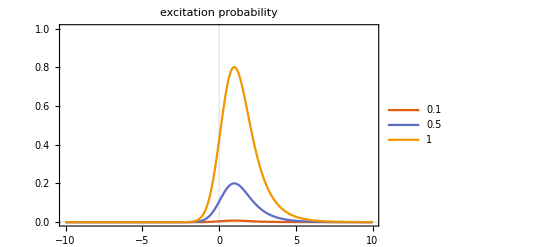

-Graphics-

```mathematica
Plot[PeHLArr,{t,tmax-2(tmax),tmax},PlotLegends->ΓpArr/Γ,PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax),tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2(tmax),tmax},PlotLegends->ΓpArr/Γ,PlotLabel->"Pulses",PlotRange->All,PlotTheme->"Scientific"]
```

#### Compare the solutions from the two methods

The plot below shows that the input-output theory Lindblad equation and Heisenberg-Langevin equations agree for all pulse shapes, except where t>2/Ω for the rectangular pulse, which is because Mathematica didn’t properly integrate it in the calculation of g(t).

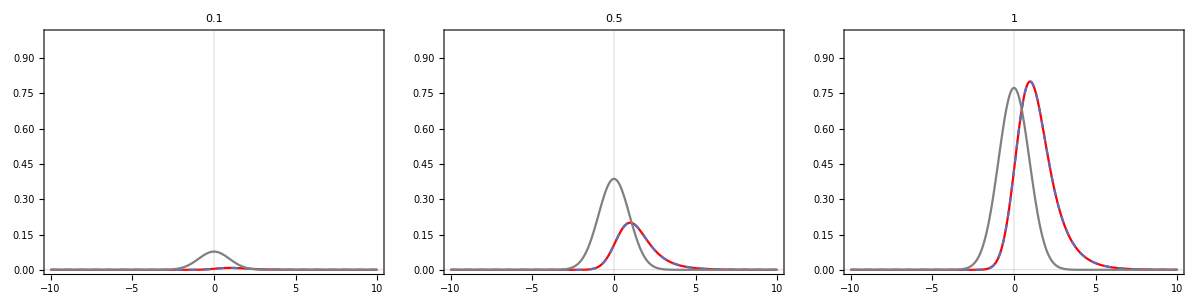

```mathematica
Grid[ArrayReshape[Table[Plot[{PeHLArr[[j]],PeLindbladArr[[j]],PulseArr[[j]]},{t,tmax-2(tmax),tmax},PlotLabel->ΓpArr[[j]],PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax),tmax},{0,1}},PlotTheme->"Scientific",PlotStyle->{Red,Dashed,Gray}],{j,Range[Length[PulseArr]]}],{1,3}]]
```

## notes and algebra

From “Quantum Liouvillian exceptional and diabolical points
for bosonic fields with quadratic Hamiltonians: The
Heisenberg-Langevin equation approach”,

which is equivalent to the operator expectation value equation below.

Considering the correspondence between 14 and 24 above, where the M matrix is the same in both, and the Liouvillian vector in the following equations, it seems reasonable to explicitly write down the four equations for ρ  and then reconstruct L and H directly from the results. The M matrix is given in Scarani, but must have the factor of -ⅈ absorbed into it. Also, σ_z=σ_1-σ_0, equivalent to the inversion ρ_ee-ρ_gg.

and,

```mathematica
Clear[ρ]
rho=Array[Subscript[ρ, #1-1,#2-1]&,{2,2}]
```

{{ρ_(0,0),ρ_(0,1)},{ρ_(1,0),ρ_(1,1)}}

The expectation values of the atomic operators give the population inversion and coherences:

```mathematica
Tr[σz.rho]
Tr[σp.rho]
Tr[σm.rho]
```

ρ_(0,0)-ρ_(1,1)

ρ_(1,0)

ρ_(0,1)

The Heisenberg-Langevin equation is then:

```mathematica
s=({{Tr[σz.rho]}, {Tr[σp.rho]}, {Tr[σm.rho]}});
M=({{-Γ, -2g, -2g*}, {0, -Γ/2, 0}, {0, 0, -Γ/2}});
b=({{-Γ}, {-g*}, {-g}});
M.s+b//TraditionalForm//MatrixForm
```

(-(Γ (ρ_(0,0)-ρ_(1,1)))-2 ρ_(0,1) Conjugate[g]-2 g ρ_(1,0)-Γ
-1/2 Γ ρ_(1,0)-Conjugate[g]
-1/2 Γ ρ_(0,1)-g)

## correspondence between operator and density matrix eqs.

### Theory of Open Quantum Systems (Heinz-Peter, Breuer and Francesco)

Work out the transformation of eq. 3.219 to eq. 3.224-3.226 using relations between the Pauli operators.

```mathematica
Clear[rho,ρ];
```

```mathematica
ρ=({{1/2(1+σ3), 1/2(σ1-ⅈ σ2)}, {1/2(σ1+ⅈ σ2), 1/2(1-σ3)}});(*the σ ops are their expectation values*)
```

```mathematica
{{ρ00dot,ρ01dot},{ρ10dot,ρ11dot}}=γ0(n+1)(σm.ρ.σp-1/2 σp.σm.ρ-1/2 ρ.σp.σm)+γ0 n(σp.ρ.σm-1/2 σm.σp.ρ-1/2 ρ.σm.σp);
{{ρ00dot,ρ01dot},{ρ10dot,ρ11dot}}//FullSimplify//MatrixForm
```

(-1/2 γ0 (1+σ3+2 n σ3) | -1/4 (1+2 n) γ0 (σ1-ⅈ σ2)
-1/4 (1+2 n) γ0 (σ1+ⅈ σ2) | 1/2 γ0 (1+σ3+2 n σ3))

```mathematica
σ3dot=ρ00dot-ρ11dot;
"dσ3/dt"
Collect[σ3dot//FullSimplify,σ3]
σ2dot=ⅈ (ρ01dot-ρ10dot);
"dσ2/dt"
Collect[σ2dot//FullSimplify,σ2]
σ1dot=(ρ01dot+ρ10dot);
"dσ1/dt"
Collect[σ1dot//FullSimplify,σ1]
```

dσ3/dt

-γ0-(1+2 n) γ0 σ3

dσ2/dt

-1/2 (1+2 n) γ0 σ2

dσ1/dt

-1/2 (1+2 n) γ0 σ1

Repeat the derivation but in the spherical basis

```mathematica
Clear[rho,ρ];
```

```mathematica
ρ=({{1/2(1+σ3), σminus}, {σplus, 1/2(1-σ3)}});(*the σ ops are their expectation values*)
```

```mathematica
{{ρ00dot,ρ01dot},{ρ10dot,ρ11dot}}=γ0(n+1)(σm.ρ.σp-1/2 σp.σm.ρ-1/2 ρ.σp.σm)+γ0 n(σp.ρ.σm-1/2 σm.σp.ρ-1/2 ρ.σm.σp);
{{ρ00dot,ρ01dot},{ρ10dot,ρ11dot}}//FullSimplify//MatrixForm
```

(-1/2 γ0 (1+σ3+2 n σ3) | -1/2 (1+2 n) γ0 σminus
-1/2 (1+2 n) γ0 σplus | 1/2 γ0 (1+σ3+2 n σ3))

```mathematica
σ3dot=ρ00dot-ρ11dot;
"dσ3/dt"
Collect[σ3dot//FullSimplify,σ3]
"dσ-/dt"
ρ01dot//FullSimplify
"dσ+/dt"
ρ10dot//FullSimplify
```

dσ3/dt

-γ0-(1+2 n) γ0 σ3

dσ-/dt

-1/2 (1+2 n) γ0 σminus

dσ+/dt

-1/2 (1+2 n) γ0 σplus

### try to reproduce Scarani using the relation from Theory of Open Quantum Systems

Try to arrive at equation 21 in Scarani by the same procedure, guessing the Hamiltonian and Lindblad operators. 

I don’t know how they get the decay vector b to have g in the 2 and 3 positions. I get these terms in the M matrix.

```mathematica
Clear[rho,ρ,g,Γ,γ];
ρ=({{1/2(1+σ3), σminus}, {σplus, 1/2(1-σ3)}});(*the σ ops are their expectation values*)
L=σm;

(*we need at least one more decay op, but it shouldn't add anything to the σ3 eq, and needs to cancel the σz terms in the σ+/- eqs*)
L2=σp;
L3=σ0;(*σm;*)
(*γ=0;*)
γ2=g;
γ3=0;
H=-ⅈ(σp g-σm g*);
{{ρ00dot,ρ01dot},{ρ10dot,ρ11dot}}=-ⅈ(H.ρ-ρ.H)+γ(L.ρ.dag[L]-1/2 dag[L].L.ρ-1/2 ρ.dag[L].L)+γ2(L2.ρ.dag[L2]-1/2 dag[L2].L2.ρ-1/2 ρ.dag[L2].L2)+
γ3(L3.ρ.dag[L3]-1/2 dag[L3].L3.ρ-1/2 ρ.dag[L3].L3);
{{ρ00dot,ρ01dot},{ρ10dot,ρ11dot}}//FullSimplify//MatrixForm
```

(1/2 (-γ (1+σ3)-g (-1+σ3+2 σplus)-2 σminus Conjugate[g]) | g σ3-1/2 (g+γ) σminus
-1/2 (g+γ) σplus+σ3 Conjugate[g] | 1/2 (γ+γ σ3+g (-1+σ3+2 σplus)+2 σminus Conjugate[g]))

```mathematica
σ3dot=ρ00dot-ρ11dot;
"dσ3/dt"
Collect[σ3dot//TraditionalForm//FullSimplify,σ3]
"dσ-/dt"
ρ01dot//TraditionalForm//FullSimplify
"dσ+/dt"
ρ10dot//TraditionalForm//FullSimplify
```

dσ3/dt

-γ (σ3+1)-2 σminus Conjugate[g]-g (σ3+2 σplus-1)

dσ-/dt

g σ3-1/2 σminus (γ+g)

dσ+/dt

σ3 Conjugate[g]-1/2 σplus (γ+g)

Arriving at the equations for the case of coherent driving is straightforward, making a reasonable guess for H and L.

```mathematica
Clear[rho,ρ,g,Γ,γ];
ρ=({{1/2(1+σ3), σminus}, {σplus, 1/2(1-σ3)}});(*the σ ops are their expectation values*)
L=σm;(*σm is decay*)
H=-ⅈ(σp g-σm g*);
{{ρ00dot,ρ01dot},{ρ10dot,ρ11dot}}=-ⅈ(H.ρ-ρ.H)+γ(L.ρ.dag[L]-1/2 dag[L].L.ρ-1/2 ρ.dag[L].L);
{{ρ00dot,ρ01dot},{ρ10dot,ρ11dot}}//FullSimplify//MatrixForm
```

(-1/2 γ (1+σ3)-g σplus-σminus Conjugate[g] | g σ3-(γ σminus)/2
-(γ σplus)/2+σ3 Conjugate[g] | 1/2 (γ+γ σ3+2 g σplus+2 σminus Conjugate[g]))

```mathematica
σ3dot=ρ00dot-ρ11dot;
"dσ3/dt"
Collect[σ3dot//FullSimplify,σ3]
"dσ-/dt"
ρ01dot//FullSimplify
"dσ+/dt"
ρ10dot//FullSimplify
(*Collect[ρ01dot//FullSimplify,σminus]
σ1dot=(ρ01dot+ρ10dot);
"dσ1/dt"
Collect[σ1dot//FullSimplify,σ1]*)
```

dσ3/dt

-γ-γ σ3-2 g σplus-2 σminus Conjugate[g]

dσ-/dt

g σ3-(γ σminus)/2

dσ+/dt

-(γ σplus)/2+σ3 Conjugate[g]

compare with:

```mathematica
({{γ (-σ3)-γ-2 σminus Conjugate[g]-2 g σplus}, {-(γ σplus)/2-Conjugate[g]}, {-(γ σminus)/2-g}})
```

```mathematica
s=({{σ3}, {σplus}, {σminus}});
M=({{-γ, -2g, -2g*}, {0, -γ/2, 0}, {0, 0, -γ/2}});
b=({{-γ}, {-g*}, {-g}});
M.s+b//TraditionalForm//MatrixForm
```

(γ (-σ3)-γ-2 σminus Conjugate[g]-2 g σplus
-(γ σplus)/2-Conjugate[g]
-(γ σminus)/2-g)

#### solve for H,L given operators eqs

more systematic than the guess and check game above?

```mathematica
(40.68+10.30+10+6.31+5+8+5.28+7.56+11+99.33-6-43.96-27)/2
```

63.25

```mathematica
203-
```

### try to reproduce Scarani using the Hamiltonian and Lindblad operator from input-output theory

The input-output theory has both atom and field in the Hilbert space, whereas the Scarani equations get rid of dependence on field operators by the end of the derivation, so it’s not entirely clear how to derive the effective Lindblad term for the Scarani equations in the reduced space.

```mathematica
Clear[rho,ρ,g,Γ,γ];
ρ=({{1/2(1+σ3), σminus}, {σplus, 1/2(1-σ3)}});(*the σ ops are their expectation values*)
L=σm;

(*we need at least one more decay op, but it shouldn't add anything to the σ3 eq, and needs to cancel the σz terms in the σ+/- eqs*)
L2=σp;
L3=σp;(*σm;*)
(*γ=0;*)
γ2=g;
γ3=1;
H=-ⅈ(σp g-σm g*);
{{ρ00dot,ρ01dot},{ρ10dot,ρ11dot}}=-ⅈ(H.ρ-ρ.H)+γ(L.ρ.dag[L]-1/2 dag[L].L.ρ-1/2 ρ.dag[L].L)+γ2(L2.ρ.dag[L2]-1/2 dag[L2].L2.ρ-1/2 ρ.dag[L2].L2)+
γ3(L3.ρ.dag[L3]-1/2 dag[L3].L3.ρ-1/2 ρ.dag[L3].L3);
{{ρ00dot,ρ01dot},{ρ10dot,ρ11dot}}//FullSimplify//MatrixForm
```

(1/2 (1-γ-(1+γ) σ3-g (-1+σ3+2 σplus)-2 σminus Conjugate[g]) | g σ3-1/2 (1+g+γ) σminus
-1/2 (1+g+γ) σplus+σ3 Conjugate[g] | 1/2 (-1+γ+σ3+γ σ3+g (-1+σ3+2 σplus)+2 σminus Conjugate[g]))

```mathematica
σ3dot=ρ00dot-ρ11dot;
"dσ3/dt"
Collect[σ3dot//TraditionalForm//FullSimplify,σ3]
"dσ-/dt"
ρ01dot//TraditionalForm//FullSimplify
"dσ+/dt"
ρ10dot//TraditionalForm//FullSimplify
```

dσ3/dt

-(γ+1) σ3-γ-2 σminus Conjugate[g]-g (σ3+2 σplus-1)+1

dσ-/dt

g σ3-1/2 σminus (γ+g+1)

dσ+/dt

σ3 Conjugate[g]-1/2 σplus (γ+g+1)

Arriving at the equations for the case of coherent driving is straightforward, making a reasonable guess for H and L.

```mathematica
Clear[rho,ρ,g,Γ,γ];
ρ=({{1/2(1+σ3), σminus}, {σplus, 1/2(1-σ3)}});(*the σ ops are their expectation values*)
L=σm;(*σm is decay*)
H=-ⅈ(σp g-σm g*);
{{ρ00dot,ρ01dot},{ρ10dot,ρ11dot}}=-ⅈ(H.ρ-ρ.H)+γ(L.ρ.dag[L]-1/2 dag[L].L.ρ-1/2 ρ.dag[L].L);
{{ρ00dot,ρ01dot},{ρ10dot,ρ11dot}}//FullSimplify//MatrixForm
```

(-1/2 γ (1+σ3)-g σplus-σminus Conjugate[g] | g σ3-(γ σminus)/2
-(γ σplus)/2+σ3 Conjugate[g] | 1/2 (γ+γ σ3+2 g σplus+2 σminus Conjugate[g]))

```mathematica
σ3dot=ρ00dot-ρ11dot;
"dσ3/dt"
Collect[σ3dot//FullSimplify,σ3]
"dσ-/dt"
ρ01dot//FullSimplify
"dσ+/dt"
ρ10dot//FullSimplify
(*Collect[ρ01dot//FullSimplify,σminus]
σ1dot=(ρ01dot+ρ10dot);
"dσ1/dt"
Collect[σ1dot//FullSimplify,σ1]*)
```

dσ3/dt

-γ-γ σ3-2 g σplus-2 σminus Conjugate[g]

dσ-/dt

g σ3-(γ σminus)/2

dσ+/dt

-(γ σplus)/2+σ3 Conjugate[g]

compare with:

```mathematica
({{γ (-σ3)-γ-2 σminus Conjugate[g]-2 g σplus}, {-(γ σplus)/2-Conjugate[g]}, {-(γ σminus)/2-g}})
```

```mathematica
s=({{σ3}, {σplus}, {σminus}});
M=({{-γ, -2g, -2g*}, {0, -γ/2, 0}, {0, 0, -γ/2}});
b=({{-γ}, {-g*}, {-g}});
M.s+b//TraditionalForm//MatrixForm
```

(γ (-σ3)-γ-2 σminus Conjugate[g]-2 g σplus
-(γ σplus)/2-Conjugate[g]
-(γ σminus)/2-g)

#### solve for H,L given operators eqs

more systematic than the guess and check game above?

```mathematica
(40.68+10.30+10+6.31+5+8+5.28+7.56+11+99.33-6-43.96-27)/2
```

63.25

```mathematica
203-
```

## classical analysis

Akbar suggested doing an overlap of the temporal shape of the pulse with that of the decay, in analogy with doing a spatial overlap integral, to see whether it agrees with the classical or quantum result.

```mathematica
tmin=-100;
tmax=10;
Clear[s,M,b,t,Ω]
g[t]=(Ω^2/(2π))^(1/4)Exp[-(Ω t)^2/4];
```

```mathematica
Integrate[g[t]^2,{t,-∞,∞}]
```

ConditionalExpression[1, Re[Ω^2]>0]

```mathematica
atom[t]=Exp[-t/2];(*Γ=1, atom decay=0 for t<0 by definition*)
Integrate[atom[t]^2,{t,0,∞}]
```

1

```mathematica
Integrate[atom[t] g[t-to],{t,0,∞},Assumptions->to>0](*limits truncated bc atom decay=0 for t<0 by definition*)
```

Integrate[ⅇ^(-t/2) g[t-to],{t,0,∞},Assumptions→to>0]

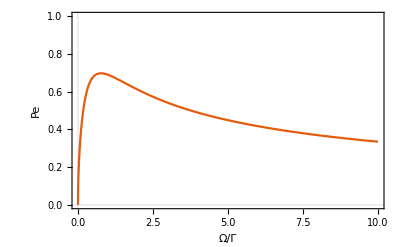

```mathematica
Plot[NIntegrate[atom[t] g[t],{t,0,∞}],{Ω,0,10},PlotTheme->"Scientific",FrameLabel->{"Ω/Γ","Pe"},PlotRange->{{0,10},{0,1}}]
```

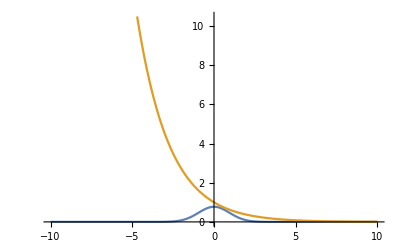

```mathematica
Plot[Evaluate[{g[t]/.Ω->1.5,atom[t]}],{t,-10,10}]
```

```mathematica
Clear[t0]
```

```mathematica
Ωsteps=Range[0,10,0.1];
t0steps=Range[-10,10,0.1];
overlapList={};
For[i=1,i<Length[Ωsteps]+1,i++,
Ω=Ωsteps[[i]];
g[t_]:=(Ω^2/(2π))^(1/4)Exp[-(Ω t)^2/4];
overlap=Max[Table[NIntegrate[atom[t] g[t-t0],{t,0,∞}],{t0,t0steps}]];
AppendTo[overlapList,overlap];
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.95306×10^-6}. NIntegrate obtained 2.51435×10^-319 and 3.×10^-323 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.95306×10^-6}. NIntegrate obtained 3.70502×10^-318 and 2.×10^-323 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0666656}. NIntegrate obtained 4.×10^-323 and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

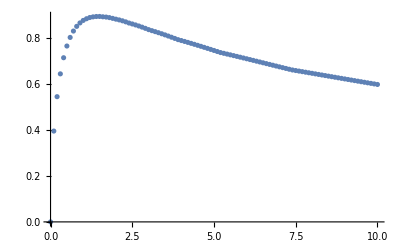

```mathematica
ListPlot[Transpose@@{{Ωsteps,overlapList}}]
```

```mathematica
Ωsteps=Range[0,10,0.1];
t0steps=Range[-10,10,0.1];
overlap0List={};
For[i=1,i<Length[Ωsteps]+1,i++,
Ω=Ωsteps[[i]];
Clear[g];
g[t_]:=(Ω^2/(2π))^(1/4)Exp[-(Ω t)^2/4];
overlap=NIntegrate[atom[t] g[t],{t,0,∞}];
AppendTo[overlap0List,overlap];
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

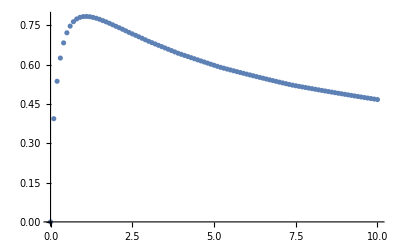

```mathematica
ListPlot[Transpose@@{{Ωsteps,(overlapList+overlap0List)/2}}]
```

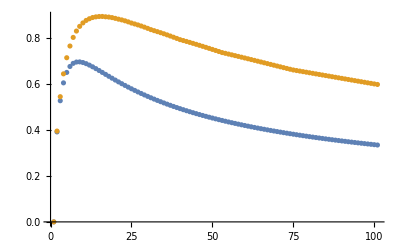

```mathematica
ListPlot[{overlap0List,overlapList}]
```